Get::noopen: Cannot open Project_rand_card.nb.

$Failed

Inserisci il numero di giocatori:

2

Inserisci il numero di carte scoperte:

4

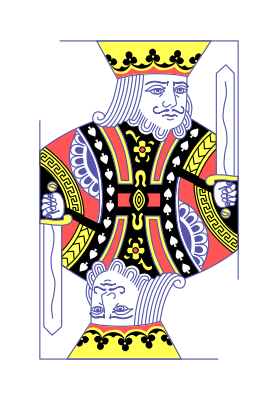
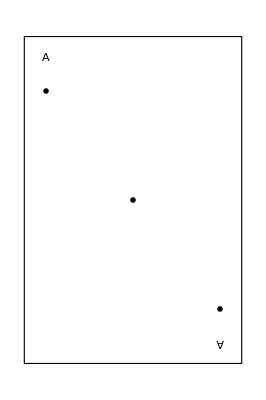
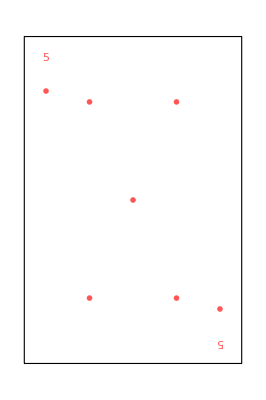
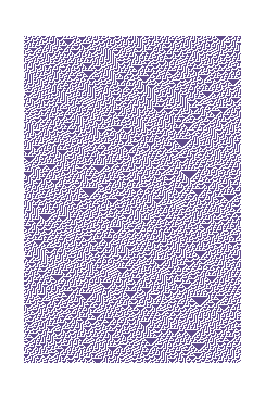
-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics-

print[qual'è la probabilità di fare coppia per il giocatore 1?]

```mathematica
Get["Project_rand_card.nb"]
Get["calcolaProb.nb"]
Print["Inserisci il numero di giocatori: "]
player=Input[]
Print["Inserisci il numero di carte scoperte: "]
carteScoperte=Input[]

{carteBanco, carteGiocatore}=randomCards[carteScoperte];
carteBanco
carteGiocatore


print["qual'è la probabilità di fare coppia per il giocatore 1?"]
Print["scegli la probabilita"]
modalita=Input[]
probabilita = calcolaProb[carteBanco, carteGiocatore, player, modalita];
```